## Now define the base basic data

```mathematica
Bases6=Association[];
```

```mathematica
Bases6["C"]=Association[];
```

```mathematica
Bases6["C","Colofour"]="colofour";
```

```mathematica
Bases6["E"]=Association[];
```

```mathematica
Bases6["E","Colofour"]="colofourrealnull";
```

```mathematica
//Bases6["G"]=Association[];
```

```mathematica
//Bases6["G","Colofour"]="colofourgenerator";
```

```mathematica
allBases6=Keys[Bases6]
```

{C,E}

```mathematica
Keys[allGraphs6[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofourrealnull,colofourgenerator}

```mathematica
Length[Bases6["G","AtomKeys"]]
```

2

```mathematica
allGraphs6[1,"colofourgenerator"]
```

ReplaceAll::reps: {ToRules[Reduce[Table[allGraphs6[k,colofourgenerator]==allGraphs6[k,colofour],{k,allGraphs6GeneratorAtomKeys}],{v1x2x3x4x5x6,v1x2x3x4x56,v1x2x3x46x5,v1x2x3x45x6,v1x2x3x456,v1x2x36x4x5,v1x2x36x45,v1x2x35x4x6,v1x2x35x46,v1x2x356x4,v1x2x34x5x6,v1x2x34x56,v1x2x346x5,v1x2x345x6,v1x2x3456,v1x26x3x4x5,v1x26x3x45,v1x26x35x4,v1x26x34x5,v1x26x345,v1x25x3x4x6,v1x25x3x46,v1x25x36x4,v1x25x34x6,v1x25x346,v1x256x3x4,v1x256x34,v1x24x3x5x6,v1x24x3x56,v1x24x36x5,v1x24x35x6,v1x24x356,v1x246x3x5,v1x246x35,v1x245x3x6,v1x245x36,v1x2456x3,v1x23x4x5x6,v1x23x4x56,v1x23x46x5,v1x23x45x6,v1x23x456,v1x236x4x5,v1x236x45,v1x235x4x6,v1x235x46,v1x2356x4,v1x234x5x6,v1x234x56,v1x2346x5,«153»}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v12345x6+v12346x5+v1234x5x6+v1235x46+v1235x4x6+v1236x45+v1236x4x5+v123x45x6+v123x46x5+v123x4x5x6+v1245x36+v1245x3x6+v1246x35+v1246x3x5+v124x35x6+v124x36x5+v124x3x5x6+v125x346+v125x34x6+v125x36x4+v125x3x46+v125x3x4x6+v126x345+v126x34x5+v126x35x4+v126x3x45+v126x3x4x5+v12x345x6+v12x346x5+v12x34x5x6+v12x35x46+v12x35x4x6+v12x36x45+v12x36x4x5+v12x3x45x6+v12x3x46x5+v12x3x4x5x6+v1345x26+v1345x2x6+v1346x25+v1346x2x5+v134x25x6+v134x26x5+v134x2x5x6+v135x246+v135x24x6+v135x26x4+v135x2x46+v135x2x4x6+v136x245+v136x24x5+v136x25x4+v136x2x45+v136x2x4x5+v13x245x6+v13x246x5+v13x24x5x6+v13x25x46+v13x25x4x6+v13x26x45+v13x26x4x5+v13x2x45x6+v13x2x46x5+v13x2x4x5x6+v145x236+v145x23x6+v145x26x3+v145x2x36+v145x2x3x6+v146x235+v146x23x5+v146x25x3+v146x2x35+v146x2x3x5+v14x235x6+v14x236x5+v14x23x5x6+v14x25x36+v14x25x3x6+v14x26x35+v14x26x3x5+v14x2x35x6+v14x2x36x5+v14x2x3x5x6+v15x2346+v15x234x6+v15x236x4+v15x23x46+v15x23x4x6+v15x246x3+v15x24x36+v15x24x3x6+v15x26x34+v15x26x3x4+v15x2x346+v15x2x34x6+v15x2x36x4+v15x2x3x46+v15x2x3x4x6+v16x2345+v16x234x5+v16x235x4+v16x23x45+v16x23x4x5+v16x245x3+v16x24x35+v16x24x3x5+v16x25x34+v16x25x3x4+v16x2x345+v16x2x34x5+v16x2x35x4+v16x2x3x45+v16x2x3x4x5+v1x2345x6+v1x2346x5+v1x234x5x6+v1x235x46+v1x235x4x6+v1x236x45+v1x236x4x5+v1x23x45x6+v1x23x46x5+v1x23x4x5x6+v1x245x36+v1x245x3x6+v1x246x35+v1x246x3x5+v1x24x35x6+v1x24x36x5+v1x24x3x5x6+v1x25x346+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x26x345+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x345x6+v1x2x346x5+v1x2x34x5x6+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x5x6/.ToRules[Reduce[Table[allGraphs6[k,colofourgenerator]==allGraphs6[k,colofour],{k,allGraphs6GeneratorAtomKeys}],{v1x2x3x4x5x6,v1x2x3x4x56,v1x2x3x46x5,v1x2x3x45x6,v1x2x3x456,v1x2x36x4x5,v1x2x36x45,v1x2x35x4x6,v1x2x35x46,v1x2x356x4,v1x2x34x5x6,v1x2x34x56,v1x2x346x5,v1x2x345x6,v1x2x3456,v1x26x3x4x5,v1x26x3x45,v1x26x35x4,v1x26x34x5,v1x26x345,v1x25x3x4x6,v1x25x3x46,v1x25x36x4,v1x25x34x6,v1x25x346,v1x256x3x4,v1x256x34,v1x24x3x5x6,v1x24x3x56,v1x24x36x5,v1x24x35x6,v1x24x356,v1x246x3x5,v1x246x35,v1x245x3x6,v1x245x36,v1x2456x3,v1x23x4x5x6,v1x23x4x56,v1x23x46x5,v1x23x45x6,v1x23x456,v1x236x4x5,v1x236x45,v1x235x4x6,v1x235x46,v1x2356x4,v1x234x5x6,v1x234x56,v1x2346x5,v1x2345x6,v1x23456,v16x2x3x4x5,v16x2x3x45,v16x2x35x4,v16x2x34x5,v16x2x345,v16x25x3x4,v16x25x34,v16x24x3x5,v16x24x35,v16x245x3,v16x23x4x5,v16x23x45,v16x235x4,v16x234x5,v16x2345,v15x2x3x4x6,v15x2x3x46,v15x2x36x4,v15x2x34x6,v15x2x346,v15x26x3x4,v15x26x34,v15x24x3x6,v15x24x36,v15x246x3,v15x23x4x6,v15x23x46,v15x236x4,v15x234x6,v15x2346,v156x2x3x4,v156x2x34,v156x24x3,v156x23x4,v156x234,v14x2x3x5x6,v14x2x3x56,v14x2x36x5,v14x2x35x6,v14x2x356,v14x26x3x5,v14x26x35,v14x25x3x6,v14x25x36,v14x256x3,v14x23x5x6,v14x23x56,v14x236x5,v14x235x6,v14x2356,v146x2x3x5,v146x2x35,v146x25x3,v146x23x5,v146x235,v145x2x3x6,v145x2x36,v145x26x3,v145x23x6,v145x236,v1456x2x3,v1456x23,v13x2x4x5x6,v13x2x4x56,v13x2x46x5,v13x2x45x6,v13x2x456,v13x26x4x5,v13x26x45,v13x25x4x6,v13x25x46,v13x256x4,v13x24x5x6,v13x24x56,v13x246x5,v13x245x6,v13x2456,v136x2x4x5,v136x2x45,v136x25x4,v136x24x5,v136x245,v135x2x4x6,v135x2x46,v135x26x4,v135x24x6,v135x246,v1356x2x4,v1356x24,v134x2x5x6,v134x2x56,v134x26x5,v134x25x6,v134x256,v1346x2x5,v1346x25,v1345x2x6,v1345x26,v13456x2,v12x3x4x5x6,v12x3x4x56,v12x3x46x5,v12x3x45x6,v12x3x456,v12x36x4x5,v12x36x45,v12x35x4x6,v12x35x46,v12x356x4,v12x34x5x6,v12x34x56,v12x346x5,v12x345x6,v12x3456,v126x3x4x5,v126x3x45,v126x35x4,v126x34x5,v126x345,v125x3x4x6,v125x3x46,v125x36x4,v125x34x6,v125x346,v1256x3x4,v1256x34,v124x3x5x6,v124x3x56,v124x36x5,v124x35x6,v124x356,v1246x3x5,v1246x35,v1245x3x6,v1245x36,v12456x3,v123x4x5x6,v123x4x56,v123x46x5,v123x45x6,v123x456,v1236x4x5,v1236x45,v1235x4x6,v1235x46,v12356x4,v1234x5x6,v1234x56,v12346x5,v12345x6,v123456}]]

## Compute keys and variables

```mathematica
MyComp:=CompareSymbols;
```

```mathematica
Monitor[Table[Bases6[base,"AtomKeys"]=Sort[Select[Keys[allGraphs6],Length[ListofVars[allGraphs6[#,Bases6[base,"Colofour"]]]]==1&],MyComp[allGraphs6[#1,Bases6[base,"Colofour"]],allGraphs6[#2,Bases6[base,"Colofour"]]]&]
,{base,allBases6}],base];
```

```mathematica
Table[Bases6[base,"Variables"]=Table[allGraphs6[k,Bases6[base,"Colofour"]],{k,Bases6[base,"AtomKeys"]}]
,{base,allBases6}];
```

```mathematica
Base6["F"]=Association[]
```

```mathematica
Base6["F","AtomKeys"]=allGraphs6
```

```mathematica
BaseCoeff6[key_,base_]:=Table[Coefficient[allGraphs6[key,Bases6[base,"Colofour"]],var],{var,Bases6[base,"Variables"]}]
```

```mathematica
BaseCoeff6[0,"E"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConversionMatrix6[base1_,base2_]:=Table[BaseCoeff6[key1,base2],{key1,Bases6[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases6[base,"AtomKeys"],{base,allBases6}]//Flatten//DeleteDuplicates//Length
```

405

```mathematica
Clear[RepGraph6];RepGraph6[base_]:=RepGraph6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->ShowGraph6Least[key],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepChromial6];RepChromial6[base_]:=RepChromial6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->ChromaticPolynomial[allGraphs6[key,"graph"],x],{key,Bases6[base,"AtomKeys"]}]
```

## Viewing come COnversion matrices

```mathematica
Table[Det[ConversionMatrix6[base1,base2]],{base1,allBases6},{base2,allBases6}]
```

{{1,1},{1,1}}

```mathematica
Table[base1->Det[ConversionMatrix6[base1,base2]]//N,{base1,allBases6},{base2,allBases6}]
```

{{C→1.,C→1.},{E→1.,E→1.}}

```mathematica
Tally[Table[Sort[Map[Length,allGraphs6[k,"vertexsets"]]],{k,allGraphs6AtomKeys}]]
```

{{{1,1,1,1,1,1},1},{{1,1,1,1,2},15},{{1,1,1,3},20},{{1,1,2,2},45},{{1,1,4},15},{{1,2,3},60},{{1,5},6},{{2,2,2},15},{{2,4},15},{{3,3},10},{{6},1}}

```mathematica
FactorInteger[196689447424]
```

{{2,9},{1459,1},{263303,1}}

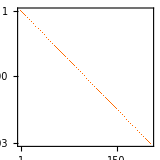
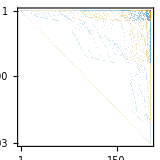
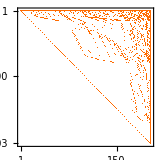
| C | E
C | -Graphics- | -Graphics-
E | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix6[base1,base2],ImageSize->160],{base1,allBases6},{base2,allBases6}],TableHeadings->{allBases6, allBases6},TableAlignments->{Center, Center}]
```

## Ranks d

```mathematica
Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[5]]}]]&]
```

{7174449,7174452,7174453,7174454,7174456,7174450,7174462,7174480,7174422,7174425,7174426,7174423,7174534,7174696,7175182,7173720,7173723,7173724,7173721,7173693,7173696,7173697,7173694,7176640,7181014,7194136,7233502,7115400,7115403,7115404,7115401,7115373,7115376,7115377,7115374,7114671,7114674,7114675,7114672,7114644,7114647,7114648,7114645,7351600,7705894,8768776,11957422}

```mathematica
MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[5]]}]]&]}]]
```

16

```mathematica
CompleteGraph[2]//EdgeList
```

{1<->2}

```mathematica
MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[2]]}]]&]}]]
```

202

```mathematica
MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[3]]}]]&]}]]
```

171

```mathematica
Monitor [Table[k->MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[k]]}]]&]}]],{k,2,6}],k]
```

{2→202,3→171,4→81,5→16,6→1}

```mathematica
Table[203-k[[2]],{k,{2->202,3->171,4->81,5->16,6->1}}]
```

{1,32,122,187,202}

```mathematica
BellB[6]-BellB[1]
```

202

```mathematica
BellB[6]-10BellB[5]+35 BellB[4]-50BellB[3]+24BellB[2]
```

6

```mathematica
BellB[6]-3BellB[5]+2 BellB[4]
```

77

```mathematica
MatrixRank[Table[BaseCoeff[k,"C"],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&Fold[And,Table[EdgeQ[allGraphs5[#,"graph"],e],{e,EdgeList[CompleteGraph[3]]}]]&]}]]
```

17

```mathematica
BellB[5]-3BellB[2]+BellB[1]
```

47

```mathematica
MatrixRank[Table[BaseCoeff[k,"C"],{k,Select[Keys[allGraphs5],EdgeQ[allGraphs5[#,"graph"],1<->2]&]}]]
```

51

```mathematica
MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],EdgeQ[allGraphs6[#,"graph"],1<->2]&]}]]
```

202

```mathematica
Select[Keys[allGraphs6],EdgeQ[allGraphs6[#,"graph"],1<->2]&]
```

26535

```mathematica
Monitor [Table[k->MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[k]]}]]&]}]],{k,2,6}],k]
```

{2→151,3→77,4→26,5→6,6→1}

```mathematica
Table[Sum[BellB[6-k]StirlingS1[n,n-k],{k,0,n-1}],{n,6}]
```

{203,151,77,26,6,1}

```mathematica
TableForm[Table[BellB[n]//FactorInteger,{n,0,10}],TableDepth->2]
```

{1,1} |  |  | 
{1,1} |  |  | 
{2,1} |  |  | 
{5,1} |  |  | 
{3,1} | {5,1} |  | 
{2,2} | {13,1} |  | 
{7,1} | {29,1} |  | 
{877,1} |  |  | 
{2,2} | {3,2} | {5,1} | {23,1}
{3,1} | {7,1} | {19,1} | {53,1}
{5,2} | {4639,1} |  |

```mathematica
Table[
Table[
StirlingS1[n,n-k],{k,0,n}
],{n,1,15}
]//TableForm
```

1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | -1 | 0 |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | -3 | 2 | 0 |  |  |  |  |  |  |  |  |  |  |  | 
1 | -6 | 11 | -6 | 0 |  |  |  |  |  |  |  |  |  |  | 
1 | -10 | 35 | -50 | 24 | 0 |  |  |  |  |  |  |  |  |  | 
1 | -15 | 85 | -225 | 274 | -120 | 0 |  |  |  |  |  |  |  |  | 
1 | -21 | 175 | -735 | 1624 | -1764 | 720 | 0 |  |  |  |  |  |  |  | 
1 | -28 | 322 | -1960 | 6769 | -13132 | 13068 | -5040 | 0 |  |  |  |  |  |  | 
1 | -36 | 546 | -4536 | 22449 | -67284 | 118124 | -109584 | 40320 | 0 |  |  |  |  |  | 
1 | -45 | 870 | -9450 | 63273 | -269325 | 723680 | -1172700 | 1026576 | -362880 | 0 |  |  |  |  | 
1 | -55 | 1320 | -18150 | 157773 | -902055 | 3416930 | -8409500 | 12753576 | -10628640 | 3628800 | 0 |  |  |  | 
1 | -66 | 1925 | -32670 | 357423 | -2637558 | 13339535 | -45995730 | 105258076 | -150917976 | 120543840 | -39916800 | 0 |  |  | 
1 | -78 | 2717 | -55770 | 749463 | -6926634 | 44990231 | -206070150 | 657206836 | -1414014888 | 1931559552 | -1486442880 | 479001600 | 0 |  | 
1 | -91 | 3731 | -91091 | 1474473 | -16669653 | 135036473 | -790943153 | 3336118786 | -9957703756 | 20313753096 | -26596717056 | 19802759040 | -6227020800 | 0 | 
1 | -105 | 5005 | -143325 | 2749747 | -37312275 | 368411615 | -2681453775 | 14409322928 | -56663366760 | 159721605680 | -310989260400 | 392156797824 | -283465647360 | 87178291200 | 0

```mathematica
TableForm[Table[
Table[Sum[BellB[max-k]StirlingS1[n,n-k],{k,0,n-1}],{n,max}],
{max,1,15}
]
]
```

1 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2 | 1 |  |  |  |  |  |  |  |  |  |  |  |  | 
5 | 3 | 1 |  |  |  |  |  |  |  |  |  |  |  | 
15 | 10 | 4 | 1 |  |  |  |  |  |  |  |  |  |  | 
52 | 37 | 17 | 5 | 1 |  |  |  |  |  |  |  |  |  | 
203 | 151 | 77 | 26 | 6 | 1 |  |  |  |  |  |  |  |  | 
877 | 674 | 372 | 141 | 37 | 7 | 1 |  |  |  |  |  |  |  | 
4140 | 3263 | 1915 | 799 | 235 | 50 | 8 | 1 |  |  |  |  |  |  | 
21147 | 17007 | 10481 | 4736 | 1540 | 365 | 65 | 9 | 1 |  |  |  |  |  | 
115975 | 94828 | 60814 | 29371 | 10427 | 2727 | 537 | 82 | 10 | 1 |  |  |  |  | 
678570 | 562595 | 372939 | 190497 | 73013 | 20878 | 4516 | 757 | 101 | 11 | 1 |  |  |  | 
4213597 | 3535027 | 2409837 | 1291020 | 529032 | 163967 | 38699 | 7087 | 1031 | 122 | 12 | 1 |  |  | 
27644437 | 23430840 | 16360786 | 9131275 | 3967195 | 1322035 | 338233 | 67340 | 10644 | 1365 | 145 | 13 | 1 |  | 
190899322 | 163254885 | 116393205 | 67310847 | 30785747 | 10949772 | 3017562 | 649931 | 111211 | 15415 | 1765 | 170 | 14 | 1 | 
1382958545 | 1192059223 | 865549453 | 516369838 | 247126450 | 93197715 | 27499083 | 6376149 | 1176701 | 175802 | 21652 | 2237 | 197 | 15 | 1

## Now for all graphs, not only with 6 vertices

```mathematica
Monitor [Table[k->MatrixRank[Table[BaseCoeff6[k,"C"],{k,Select[Keys[allGraphs6],Fold[And,Table[EdgeQ[allGraphs6[#,"graph"],e],{e,EdgeList[CompleteGraph[k]]}]]&]}]],{k,2,6}],k]
```

{2→202,3→171,4→81,5→16,6→1}

```mathematica
Table[203-k[[2]],{k,{2->202,3->171,4->81,5->16,6->1}}]
```

{1,32,122,187,202}